# Fit vertex angles in experiments, measure domain sizes, and the number of vertices (corners) of each domain

```mathematica
movie=Import[ParentDirectory@ParentDirectory@ParentDirectory[NotebookDirectory[]]<>"/GlockEtAl-RawData/180427_ch1_2uM-MinD_8uM-E-His_timeseries01.lsm"][[1,All,1]];
```

Time in seconds, starting counting at the first snapshot.

```mathematica
times=10Range[0,99];
```

Separate MinD and MinE channels

```mathematica
movieSep=(ColorSeparate[#])&/@movie;
```

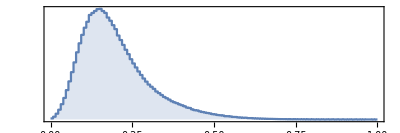
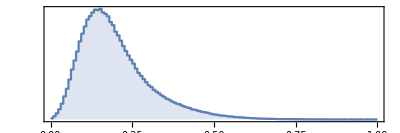
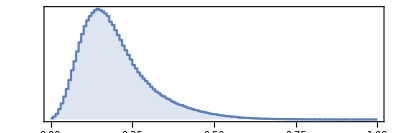
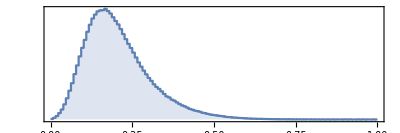
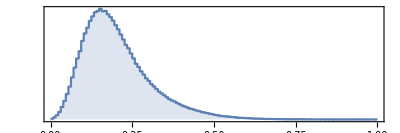
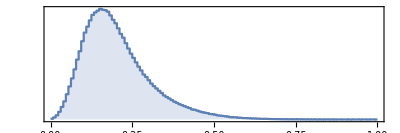
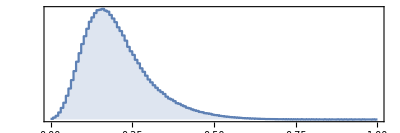
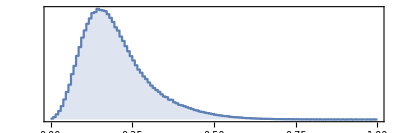

```mathematica
ImageHistogram/@ImageAdjust/@movieSep[[All,1]]
```

```mathematica
movieReg={ImageAdjust[ImageAdjust@#[[1]],0,{0,0.5}],ImageAdjust@#[[2]]}&/@movieSep;
```

Color scheme RGB

```mathematica
colorMap={minD,minE,minE+minD/1.5};
```

## Movie export

```mathematica
ClearAll@frame;
frame[i_]:=Show[ImageResize[ColorCombine[Image/@#,"RGB"]&@((colorMap/.{minD->#[[2]],minE->#[[1]]})&@(ImageData/@ImageAdjust/@movieReg[[i]])),500],
Graphics[{EdgeForm[{White}],FaceForm[],RegularPolygon[{145,72},15,5],
RegularPolygon[{345,160},15,4],
RegularPolygon[{366,198},15,4],
RegularPolygon[{413,170},20,4],
RegularPolygon[{426,32},15,5],
RegularPolygon[{490,358},15,4],
RegularPolygon[{268,345},15,5],
RegularPolygon[{478,490},15,4],
RegularPolygon[{138,465},15,4],
RegularPolygon[{445,180},15,4]
}],
Graphics[{White,Thick,Line[{#,#+{-10,10}}&@{258,458}],
Line[{#,#+{-10,0}}&@{230,452}],
Line[{#,#+{0,10}}&@{268,278}],
Line[{#,#+{10,-10}}&@{245,135}],
Line[{#,#+{10,-10}}&@{160,360}],
Line[{#,#+{10,5}}&@{110,190}],
Line[{#,#+{0,10}}&@{400,435}]
}],
ImageSize->500
];
```

```mathematica
ClearAll@renderFrame;
renderFrame[i_]:=Grid[{
{Row[{Style["t",Italic,Black],Style[" = "<>ToString[times[[i]],TraditionalForm]<>"s",Black],Style["  MinD ",RGBColor[{1,0,1/1.5}/1.5]],Style["MinE",RGBColor[{0,1,1}/1.5]]},ImageMargins->10]},
{frame[i]}
},
Spacings->{0,0},
Background->White
]
```

```mathematica
renderFrame[100]
```

t = 990s  MinD MinE
-Graphics-

```mathematica
Export[
NotebookDirectory[]<>"movie/frame001.png",
Table[
Magnify[renderFrame[t],1.516],(* there is a reason for this weird choice of the magnification factor *)
{t,1,100}
],
"VideoFrames"
];
```

## Example collapse

Length unit per pixel [µm]

```mathematica
dx=0.2125481;
```

```mathematica
ClearAll@frame5c;
frame5c[i_]:=ImageTrim[ColorCombine[Image/@#,"RGB"]&@((colorMap/.{minD->#[[2]],minE->#[[1]]})&@(ImageData/@ImageAdjust/@movieReg[[i]])),2{{125,52},{165,92}}]
```

```mathematica
ind=1;
times[[ind]]
frame5c[ind]
```

0

-Graphics-

```mathematica
ind=4;
times[[ind]]
frame5c[ind]
```

30

-Graphics-

```mathematica
ind=7;
times[[ind]]
frame5c[ind]
```

60

-Graphics-

```mathematica
ind=10;
times[[ind]]
frame5c[ind]
```

90

-Graphics-

```mathematica
Export[NotebookDirectory[]<>"evolutionExp-collapse-5corners.pdf",Grid[{{frame5c[1],frame5c[4],frame5c[7],frame5c[10]}}]];
```

```mathematica
ClearAll@frame4c;
frame4c[i_]:=ImageTrim[ColorCombine[Image/@#,"RGB"]&@((colorMap/.{minD->#[[2]],minE->#[[1]]})&@(ImageData/@ImageAdjust/@movieReg[[i]])),2{{346,178},{386,218}}]
```

```mathematica
ind=1;
times[[ind]]
frame4c[ind]
```

0

-Graphics-

```mathematica
ind=11;
times[[ind]]
frame4c[ind]
```

100

-Graphics-

```mathematica
ind=16;
times[[ind]]
frame4c[ind]
```

150

-Graphics-

```mathematica
ind=21;
times[[ind]]
frame4c[ind]
```

200

-Graphics-

```mathematica
ind=26;
times[[ind]]
frame4c[ind]
```

250

-Graphics-

```mathematica
Export[NotebookDirectory[]<>"evolutionExp-collapse-4corners.pdf",Grid[{{frame4c[11],frame4c[16],frame4c[21],frame4c[26]}}]];
```

## Example splitting

```mathematica
ClearAll@frameS;
frameS[i_]:=ImageTrim[ColorCombine[Image/@#,"RGB"]&@((colorMap/.{minD->#[[2]],minE->#[[1]]})&@(ImageData/@ImageAdjust/@movieReg[[i]])),2{{370,420},{420,470}}]
```

```mathematica
ind=41;
times[[ind]]
frameS[ind]
```

400

-Graphics-

```mathematica
ind=51;
times[[ind]]
frameS[ind]
```

500

-Graphics-

```mathematica
ind=61;
times[[ind]]
frameS[ind]
```

600

-Graphics-

```mathematica
ind=71;
times[[ind]]
frameS[ind]
```

700

-Graphics-

```mathematica
Export[NotebookDirectory[]<>"evolutionExp-splitting-1.pdf",Grid[{{frameS[41],frameS[51],frameS[61],frameS[71]}}]];
```

```mathematica
ClearAll@frameS2;
frameS2[i_]:=ImageTrim[ColorCombine[Image/@#,"RGB"]&@((colorMap/.{minD->#[[2]],minE->#[[1]]})&@(ImageData/@ImageAdjust/@movieReg[[i]])),2{{210,430},{275,495}}]
```

```mathematica
ind=21;
times[[ind]]
frameS2[ind]
```

200

-Graphics-

```mathematica
ind=31;
times[[ind]]
frameS2[ind]
```

300

-Graphics-

```mathematica
ind=41;
times[[ind]]
frameS2[ind]
```

400

-Graphics-

```mathematica
ind=51;
times[[ind]]
frameS2[ind]
```

500

-Graphics-

```mathematica
Export[NotebookDirectory[]<>"evolutionExp-splitting-2.pdf",Grid[{{frameS2[21],frameS2[31],frameS2[41],frameS2[51]}}]];
```